{{0,-1},{0,1},{-1,-1},{0,-2},{1,-2},{1,1},{1,-1},{0,2},{2,-2},{-2,-1},{0,3},{-3,-1},{2,-3},{2,-4},{-4,-1},{1,-4},{3,-2},{-1,3},{3,-4},{0,-4},{-4,0},{2,1},{2,-5},{0,-5},{0,-6},{-5,-1},{4,-4},{-6,-1},{-1,4},{-3,-2},{1,3},{-2,4},{2,-6},{3,1},{-7,-1},{4,1},{2,-7},{3,-1},{-4,-2},{5,-4},{3,2},{-8,-1},{-9,-1},{5,1},{-7,0},{6,1},{2,-8},{2,-9},{-10,-1},{2,-10},{-8,-2},{-11,-1},{-11,0},47894,{-226,-83},{-195,13},{-285,-22},{-124,224},{169,192},{207,43},{-30,287},{41,-87},{-16,-277},{12,43},{162,-132},{270,-22},{-188,165},{124,-296},{172,179},{112,65},{-202,85},{-185,-152},{-250,24},{59,216},{243,123},{219,-127},{-221,187},{162,-134},{-287,128},{24,-262},{147,42},{-188,166},{-252,116},{278,-90},{-28,-33},{2,211},{149,-207},{-26,294},{-197,116},{110,237},{-113,223},{-245,146},{-33,61},{-228,42},{-45,-179},{-127,-8},{142,202},{79,283},{140,214},{82,-67},{267,93},{229,-15},{-35,-45},{-136,-171},{283,-91},{-221,188},{-226,185}}
 |  |  |  |

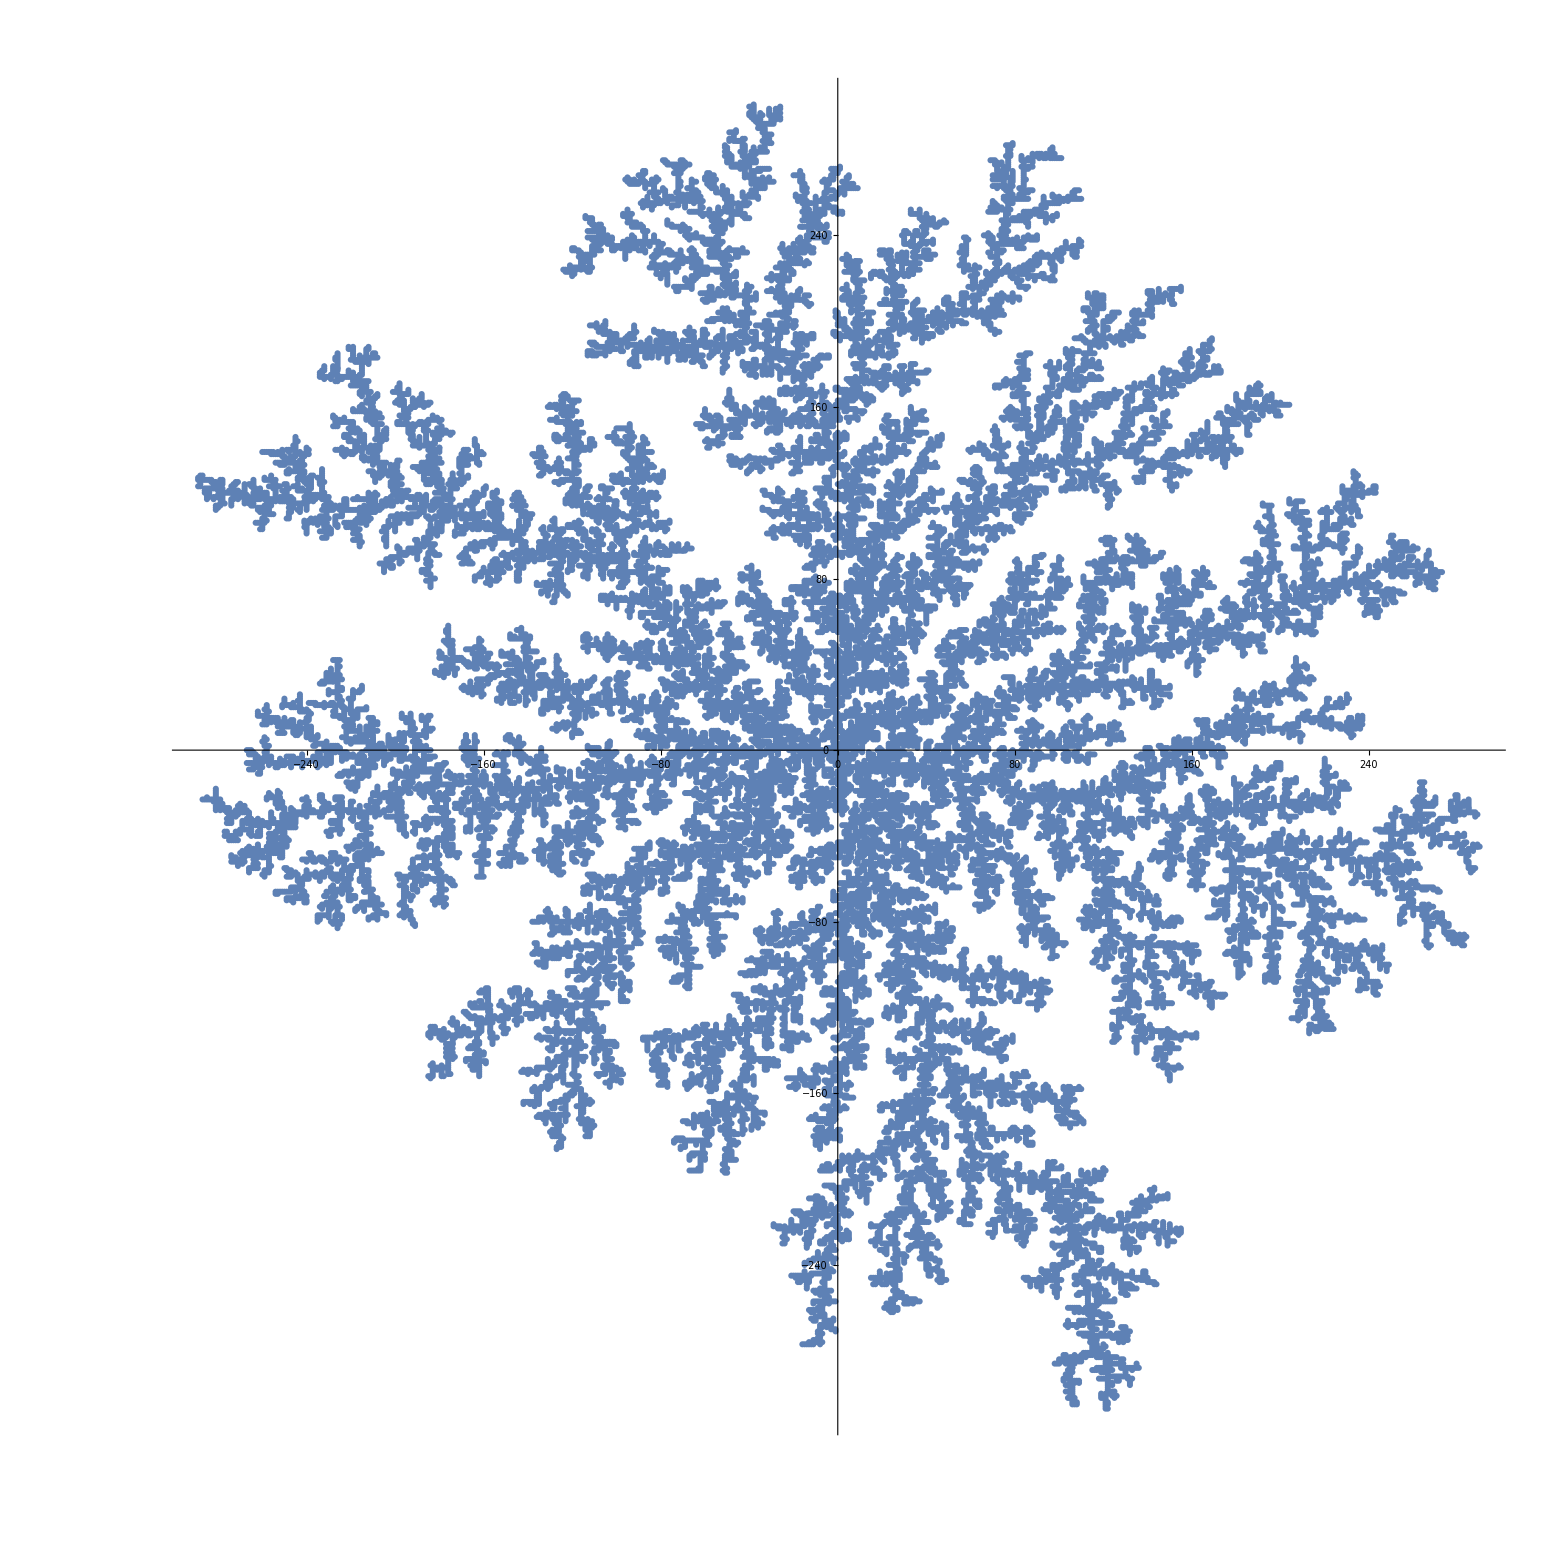

```mathematica
a=Import["D:\\Desktop\\Computing  Physics\\homework11\\test.dat"]
ListPlot[a,AspectRatio->1]
```

```mathematica
Count[a,{u_,v_}/;-50<u<50/;-50<v<50]
```

4437

```mathematica
t={{Log[50],Log[4437]},{Log[60],Log[6155]},{Log[70],Log[7889]},
{Log[80],Log[9753]},
{Log[90],Log[11701]},{Log[100],Log[13600]},{Log[120],Log[18019]},{Log[150],Log[25170]},{Log[200],Log[36111]}}
```

{{Log[50],Log[4437]},{Log[60],Log[6155]},{Log[70],Log[7889]},{Log[80],Log[9753]},{Log[90],Log[11701]},{Log[100],Log[13600]},{Log[120],Log[18019]},{Log[150],Log[25170]},{Log[200],Log[36111]}}

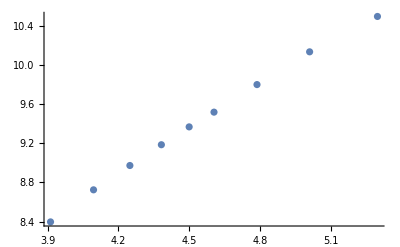

```mathematica
b=ListPlot[t]
```

```mathematica
Fit[t,{1,x},x]
```

2.53039+1.51378 x

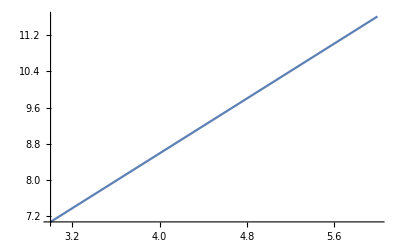

```mathematica
d=Plot[2.5303857781595105+1.5137753898550934 x,{x,3,6}]
```

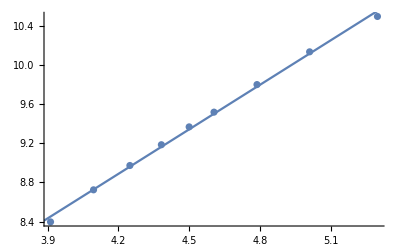

```mathematica
Show[b,d]
```

```mathematica
e=Fit[t,{1,x,x^2,x^3},x]
```

0.435548+2.12911 x+0.0323756 x^2-0.0142927 x^3

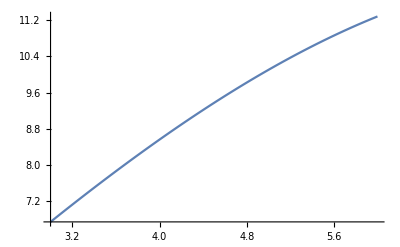

```mathematica
f=Plot[e,{x,3,6}]
```

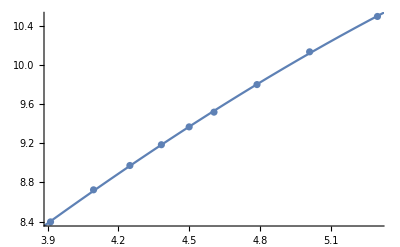

```mathematica
Show[b,f]
```